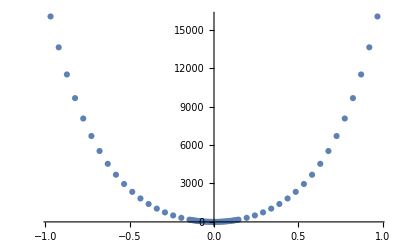

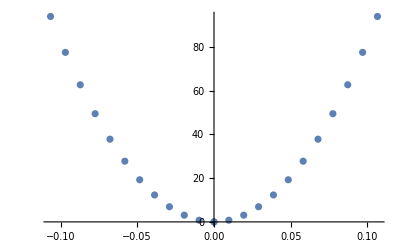

```mathematica
(*H.J.Korsch and M Glück,"Computing quantum eigenvalues made easy" Eur.J.Phys.23 (2002) 413-426.
ftp://ftp.physics.uwa.edu.au/pub/Computational/References/Korsch%20and%20Gluck.pdf
*)
ClearAll;
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC"];
filesEinsteinPot={"Zr_3200K_energy_displacement","Zr_3200K_energy_displacement_harmonic"};
ZirconiumPotentialEinstein=ReadList[filesEinsteinPot[[1]],{Number, Number}];
ZirconiumPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[2]],{Number, Number}];
Show@ListPlot@ZirconiumPotentialEinstein
Show@ListPlot@ZirconiumPotentialEinsteinHarmonic
```

```mathematica
(*Polynomial fit]*)
(*secondOrderFit=Fit[CarbonPotentialEinsteinHarmonic,{x^2},x]*)
V[2,x_]:=Fit[ZirconiumPotentialEinsteinHarmonic,{x^2},x]
```

```mathematica
V[4,x_]:=Fit[ZirconiumPotentialEinstein,{x^2,x^4},x]
V[6,x_]:=Fit[ZirconiumPotentialEinstein,{x^2,x^4,x^6},x]
V[8,x_]:=Fit[ZirconiumPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[10,x_]:=Fit[ZirconiumPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
```

```mathematica
V[2,x]
```

8248.72 x^2

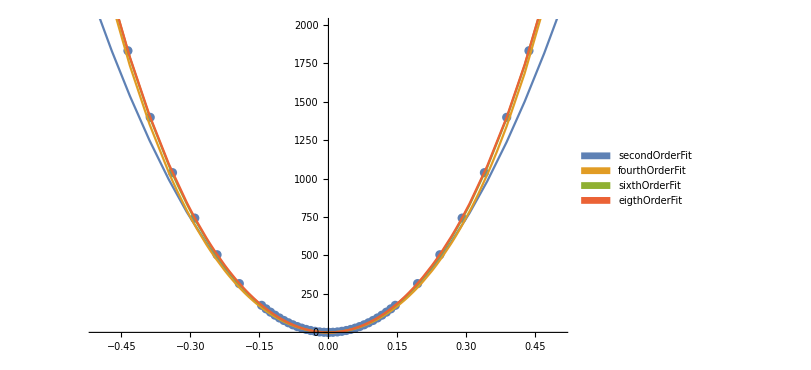

```mathematica
nOrderFit={secondOrderFit,fourthOrderFit,sixthOrderFit,eigthOrderFit,tenthOrderFit};
Show[{ListPlot[ZirconiumPotentialEinstein,ImageSize->600, PlotRange->{{-0.5,0.5},{0,2000
}}],Plot[Evaluate@{V[2,x],V[4,x],V[6,x],V[8,x]},{x,-1,1},PlotLegends->SwatchLegend[nOrderFit]]}]
```

```mathematica
ZirconiumPotentialEinstein//MatrixForm;
ZirconiumPotentialEinsteinHarmonic//MatrixForm;
```

```mathematica
(*Units*)
"ℏ=m=1;(ℏ^2/(2*m))";
```

```mathematica
(*Code*)
"Position basis potential operator matrix";
xOp[dim_]:=SparseArray[{Band[{1,2}]->#,Band[{2,1}]->#},{#,#}&@dim]&[Table[Sqrt[i],{i,dim-1}]/Sqrt[2]]

"Laplacian operator expressed as a sparse tri-diagonal-ish matrix";
eKin[dim_]:=1/2 SparseArray[{Band[{1,1}]->Table[i-1/2,{i,dim}],Band[{1,3}]->#,Band[{3,1}]->#},{#,#}&@dim]&[Table[-Sqrt[i (i+1)/2],{i,dim-2}]/Sqrt[2]]
MatrixForm[xOp[8]];
MatrixForm[eKin[8]];

(*Hamiltonian matrix operators for 1-d Schrodinger equation - basis schown for 2-8*)
Table[{MatrixForm[xOp[i]],MatrixForm[eKin[i]]},{i,3,8}]//MatrixForm;
```

```mathematica
"spectrum[n,tolerance][potential,var] solve the eigensystem for n eigenvalues and vectors. The number of basis states is determined to"
spectrum[n_,tolerance_: .001][potential_,var_]/;PolynomialQ[potential,var]:=Module[{x,h,e,v,c=CoefficientList[potential,var],min=First@Check[Minimize[potential,var],Print["No absolute potential minimum found. Make sure the leading power has a positive coefficient!"];
Abort[],Minimize::natt]},FixedPoint[{#[[1]]+1,Eigenvalues[h=1/90*eKin[#[[1]]]+N[Sum[c[[i]] MatrixPower[xOp[#[[1]]],i-1],{i,2,Length[c]}]+(c[[1]]-min) IdentityMatrix[#[[1]]]],-n]}&,{n+1,2 Reverse@Range[n]-1},SameTest->(Max@Abs[#1[[2]]-#2[[2]]]<tolerance&)];
{e,v}=Reverse/@Eigensystem[h,-n];
{e+min,ψe/@v}]
```

spectrum[n,tolerance][potential,var] solve the eigensystem for n eigenvalues and vectors. The number of basis states is determined to

```mathematica
Format[ψe[l_List]]:=ψe[Row[{"«",Length[l],"»"}]]
ψe[l_List][x_]:=1/(Pi^(1/4))Exp[-x^2/2] l.(1/Sqrt[2^# #!] HermiteH[#,x]&[Range[Length[l]]-1])

plotSpectrum[data_,potential_,{var_,min_,max_}]:=Show[Apply[Plot[Evaluate[#1+(Last[#1]-First[#1])/(2+Length[#1])/2 Through[#2[var]]],{var,min,max},PlotLegends->SwatchLegend[data],Prolog->{Gray,Map[Line[{{min,#},{max,#}}]&,#1]},Frame->True]&,data],Plot[potential,{var,min,max}]]
```

```mathematica
(*2nd order fit system*)
1/1000*V[2,x]
v2=spectrum[3][1/1000*V[2,x],x]
```

8.24872 x^2

{{0.214069,0.642249,1.06983},{ψe[«269»],ψe[«269»],ψe[«269»]}}

```mathematica
With[{v=1/1000*V[2,x],n=10},plotSpectrum[spectrum[n][v,x],v,{x,-2,2}]]
```

5.87509 x^2

{{0.180664,0.541991,0.903319,1.26465,1.62597,1.9873,2.34863,2.70994,3.07138,3.43209},{ψe[«506»],ψe[«506»],ψe[«506»],ψe[«506»],ψe[«506»],ψe[«506»],ψe[«506»],ψe[«506»],ψe[«506»],ψe[«506»]}}

$Aborted

(5434.81 x^2+7694.76 x^4)/1000

{{2.00462,6.50664,11.8226,17.7143,24.0756,30.8397,37.96,45.4015,53.1368,61.1436},{ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»],ψe[«120»]}}

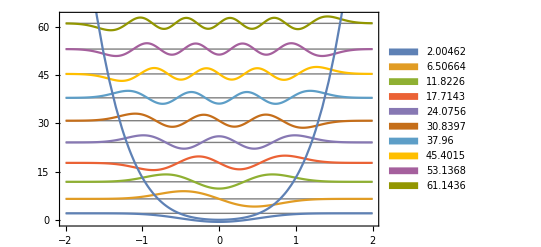

```mathematica
(*4th order fit system*)
1/1000*V[4,x]
v4=spectrum[10][0.001*V[4,x],x]
With[{v=0.001*V[4,x],n=10},plotSpectrum[spectrum[n][v,x],v,{x,-2,2}]]
```

(5883.95 x^2+6040.02 x^4+1328.35 x^6)/1000

{{2.01983,6.52634,11.8497,17.8165,24.335,31.3446,38.8012,46.6709,54.9268,63.5458},{ψe[«119»],ψe[«119»],ψe[«119»],ψe[«119»],ψe[«119»],ψe[«119»],ψe[«119»],ψe[«119»],ψe[«119»],ψe[«119»]}}

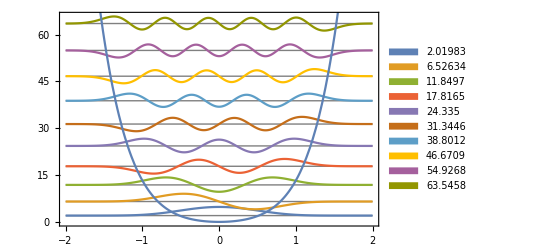

```mathematica
(*6th order fit system*)
1/1000*V[6,x]
v6=spectrum[10][0.001*V[6,x],x]
With[{v=0.001*V[6,x],n=10},plotSpectrum[spectrum[n][v,x],v,{x,-2,2}]]
```

(5855.41 x^2+6235.05 x^4+954.932 x^6+213.372 x^8)/1000

{{2.01944,6.52691,11.8535,17.8289,24.369,31.4192,38.9404,46.9023,55.2809,64.0561},{ψe[«118»],ψe[«118»],ψe[«118»],ψe[«118»],ψe[«118»],ψe[«118»],ψe[«118»],ψe[«118»],ψe[«118»],ψe[«118»]}}

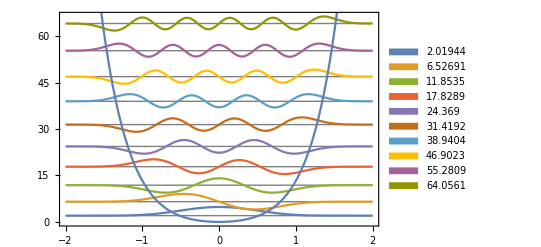

```mathematica
(*8th order fit system*)
1/1000*V[8,x]
v8=spectrum[10][0.001*V[8,x],x]
With[{v=0.001*V[8,x],n=10},plotSpectrum[spectrum[n][v,x],v,{x,-2,2}]]
```

(5887.62 x^2+5880.89 x^4+2145.94 x^6-1347.89 x^8+699.638 x^10)/1000

{{2.01991,6.5289,11.8639,17.8673,24.4761,31.6666,39.4287,47.7563,56.6432,66.0829},{ψe[«132»],ψe[«132»],ψe[«132»],ψe[«132»],ψe[«132»],ψe[«132»],ψe[«132»],ψe[«132»],ψe[«132»],ψe[«132»]}}

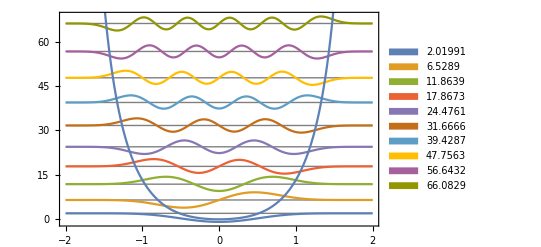

```mathematica
(*10th order fit system*)
1/1000*V[10,x]
v10=spectrum[10][0.001*V[10,x],x]
With[{v=0.001*V[10,x],n=10},plotSpectrum[spectrum[n][v,x],v,{x,-2,2}]]
```

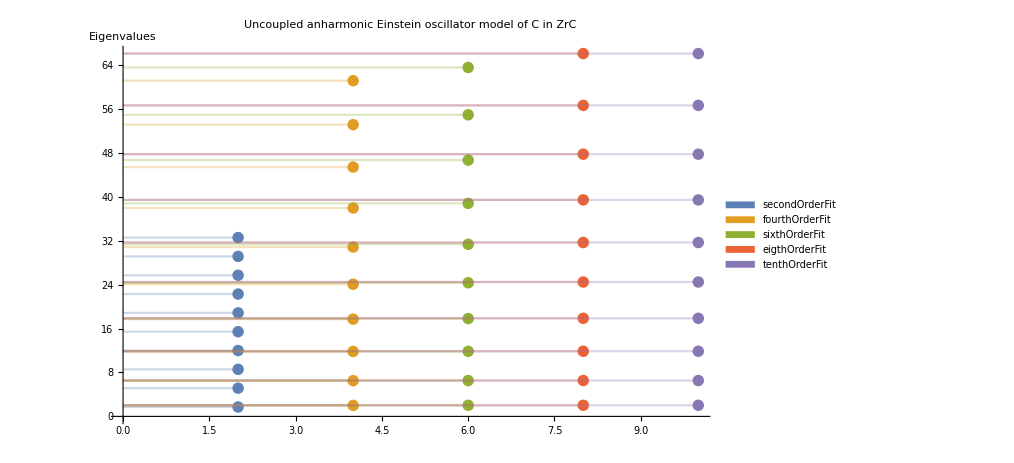

```mathematica
v={v2,v4,v6,v8,v10};
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{axisOrigin,#2},{#1,#2}}&@@@a]};
horizontalListPlotFill@ListPlot[Table[Table[{j*2i/i,v[[j]][[1]][[i]]},{i,1,10}],{j,1,5}],AxesOrigin->{0,0},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Uncoupled anharmonic Einstein oscillator model of C in ZrC",AxesLabel->{"","Eigenvalues"},ImageSize->750]
```

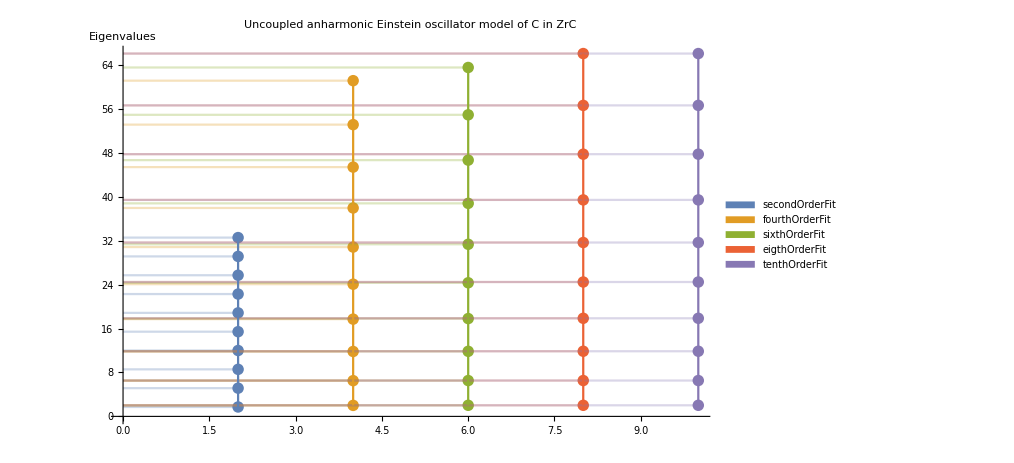

```mathematica
Show[horizontalListPlotFill@ListPlot[Table[Table[{j*2i/i,v[[j]][[1]][[i]]},{i,1,10}],{j,1,5}],AxesOrigin->{0,0},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Uncoupled anharmonic Einstein oscillator model of C in ZrC",AxesLabel->{"","Eigenvalues"},ImageSize->750],horizontalListPlotFill@ListPlot[Table[Table[{j*2i/i,v[[j]][[1]][[i]]},{i,1,10}],{j,1,5}],AxesOrigin->{0,0},Joined->True,PlotLabel->"Uncoupled anharmonic Einstein oscillator model of C in ZrC",AxesLabel->{"","Eigenvalues"},ImageSize->750]]
```